```mathematica
SetDirectory[NotebookDirectory[]];
Get["eigenfaces-algorithm.m"]
```

```mathematica
makeGrid[trainingData_,testData_,numEF_]:=Module[{},
neutralFaces=trainingData[[All,1]];
normalizedFaces=Map[#-Mean[#]&, Flatten/@trainingData[[All,1]]];
{eigenvalues, eigenfaces}=findEigenfaces[normalizedFaces];
trainingFaces=Map[eigenCompress[#,eigenfaces,numEF]&,normalizedFaces];
Grid@Table[Join[{Image[face[[1]]],"→"},matches=recognizeFace[face[[1]],numEF,1][[1]];trainingData[[matches,2]]],{face,testData}]
]
```

```mathematica
FOM[trainingData_,testData_,numEF_/;NumberQ[numEF]]:=Module[{},
FOM[trainingData,testData,{numEF,numEF}][[1]]
]
```

```mathematica
FOM[trainingData_,testData_,{numEFmin_,numEFmax_}]:=Module[{},
FOM[trainingData,trainingData,testData,{numEFmin,numEFmax}]
]
```

```mathematica
FOM[trainingData_List,eigenTraining_List,testData_List,{numEFmin_,numEFmax_}]:=Module[{allTrainingFaces,successpercent,successpercents},
neutralFaces=eigenTraining[[All,1]];
normalizedFaces=Map[#-Mean[#]&, Flatten/@eigenTraining[[All,1]]];
{eigenvalues, eigenfaces}=findEigenfaces[normalizedFaces];

(* Switch to using full training data *)
normalizedFaces=Map[#-Mean[#]&, Flatten/@trainingData[[All,1]]];
allTrainingFaces=Map[eigenCompress[#,eigenfaces,numEFmax]&,normalizedFaces];

(* Compute the success percentages for each numEF *)
successpercents=Table[
trainingFaces=allTrainingFaces[[All,1;;numEF]];
matchesFound=Table[{face[[2]],trainingData[[recognizeFace[face[[1]],numEF,1][[1,1]]]][[2]]},{face,testData}];
successpercent=(Length@Cases[matchesFound,{x_,x_}])/(Length@matchesFound),{numEF,numEFmin,numEFmax}];
confidences=Table[
trainingFaces=allTrainingFaces[[All,1;;numEF]];
matches=Table[{face,recognizeFace[face[[1]],numEF,2][[1]]},{face,testData}];
confidenceInterval=Mean[
Table[
If[match[[1,2]]==trainingData[[match[[2,1]]]][[2]],
(* The first guess was correct *)
EuclideanDistance[match[[2,1]],match[[1,1]]]-EuclideanDistance[match[[2,2]],match[[1,1]]]
,(* else *)

]
,{match,matches}]
]


,
{numEF,numEFmin,numEFmax}];
Return[successpercents]
]
```

```mathematica
Table[i,{i,10,5,-1}]
```

# Neutral faces training

```mathematica
labelledFaces=MapThread[Labeled[#1,#2]&,{images,Catenate@Transpose@ConstantArray[names,8]}];
```

## Train on 43, test on 301 (sampled)

```mathematica
training=labelledFaces[[1;;344;;8]];testing=labelledFaces[[Complement[Range[344],Range[344,8]]]];
```

```mathematica
data=Table[FOM[training,testing[[s;;All;;7]],{1,43}],{s,1,7}];
Dimensions@data
```

{7,43}

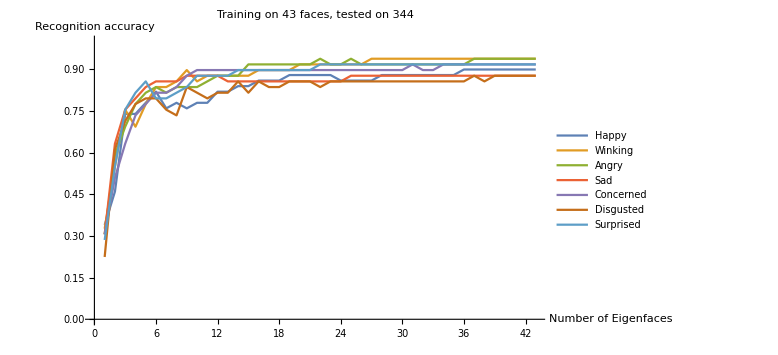

```mathematica
ListLinePlot[data,PlotRange->{{0,All},{0,1}},PlotLegends->emotions[[2;;8]],ImageSize->Large,AxesLabel->{"Number of Eigenfaces","Recognition accuracy"},PlotLabel->"Training on "<>ToString@Length@training<>" faces, tested on "<>ToString@Length@testing]
```

```mathematica
makeGrid[training,testing,All]
```

-Graphics- | → | Ariana
-Graphics- | → | Ariana
-Graphics- | → | Ariana
-Graphics- | → | Ariana
-Graphics- | → | Ariana
-Graphics- | → | Ariana
-Graphics- | → | Ariana
-Graphics- | → | Ariana
-Graphics- | → | Bryan
-Graphics- | → | Bryan
-Graphics- | → | Bryan
-Graphics- | → | Max
-Graphics- | → | Bryan
-Graphics- | → | Bryan
-Graphics- | → | Jonah
-Graphics- | → | Bryan
-Graphics- | → | Charlie
-Graphics- | → | Charlie
-Graphics- | → | Charlie
-Graphics- | → | Charlie
-Graphics- | → | Charlie
-Graphics- | → | Charlie
-Graphics- | → | Charlie
-Graphics- | → | Charlie
-Graphics- | → | Chloe
-Graphics- | → | Chloe
-Graphics- | → | Chloe
-Graphics- | → | Chloe
-Graphics- | → | Chloe
-Graphics- | → | Chloe
-Graphics- | → | Chloe
-Graphics- | → | Chloe
-Graphics- | → | Chris
-Graphics- | → | Chris
-Graphics- | → | Chris
-Graphics- | → | Chris
-Graphics- | → | Chris
-Graphics- | → | Chris
-Graphics- | → | Ariana
-Graphics- | → | Chris
-Graphics- | → | Danny
-Graphics- | → | Danny
-Graphics- | → | Danny
-Graphics- | → | Danny
-Graphics- | → | Jonah
-Graphics- | → | Jonah
-Graphics- | → | Jonah
-Graphics- | → | Chloe
-Graphics- | → | David
-Graphics- | → | David
-Graphics- | → | David
-Graphics- | → | David
-Graphics- | → | David
-Graphics- | → | David
-Graphics- | → | David
-Graphics- | → | David
-Graphics- | → | Dhash
-Graphics- | → | Dhash
-Graphics- | → | Dhash
-Graphics- | → | Dhash
-Graphics- | → | Dhash
-Graphics- | → | Dhash
-Graphics- | → | Eric
-Graphics- | → | Chris
-Graphics- | → | Diego
-Graphics- | → | Diego
-Graphics- | → | Diego
-Graphics- | → | Diego
-Graphics- | → | Diego
-Graphics- | → | Diego
-Graphics- | → | Diego
-Graphics- | → | Diego
-Graphics- | → | Emily
-Graphics- | → | Emily
-Graphics- | → | Emily
-Graphics- | → | Emily
-Graphics- | → | Emily
-Graphics- | → | Emily
-Graphics- | → | Emily
-Graphics- | → | Emily
-Graphics- | → | Eric
-Graphics- | → | Eric
-Graphics- | → | Eric
-Graphics- | → | Eric
-Graphics- | → | Eric
-Graphics- | → | Eric
-Graphics- | → | Eric
-Graphics- | → | Eric
-Graphics- | → | Gwen
-Graphics- | → | Gwen
-Graphics- | → | Gwen
-Graphics- | → | Gwen
-Graphics- | → | Gwen
-Graphics- | → | Gwen
-Graphics- | → | Gwen
-Graphics- | → | Gwen
-Graphics- | → | Harper
-Graphics- | → | Harper
-Graphics- | → | Harper
-Graphics- | → | Harper
-Graphics- | → | Harper
-Graphics- | → | Harper
-Graphics- | → | Harper
-Graphics- | → | John
-Graphics- | → | Isaac
-Graphics- | → | Isaac
-Graphics- | → | Isaac
-Graphics- | → | Isaac
-Graphics- | → | Isaac
-Graphics- | → | Isaac
-Graphics- | → | Isaac
-Graphics- | → | Isaac
-Graphics- | → | Izzy
-Graphics- | → | Izzy
-Graphics- | → | Izzy
-Graphics- | → | Izzy
-Graphics- | → | Izzy
-Graphics- | → | Izzy
-Graphics- | → | Izzy
-Graphics- | → | Izzy
-Graphics- | → | Jared
-Graphics- | → | Jared
-Graphics- | → | Jared
-Graphics- | → | Jared
-Graphics- | → | Jared
-Graphics- | → | Jared
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | Jonah
-Graphics- | → | Jonah
-Graphics- | → | Jonah
-Graphics- | → | Jonah
-Graphics- | → | Jonah
-Graphics- | → | Jonah
-Graphics- | → | Chris
-Graphics- | → | Jonah
-Graphics- | → | Kaitlyn
-Graphics- | → | Kaitlyn
-Graphics- | → | Kaitlyn
-Graphics- | → | Kaitlyn
-Graphics- | → | Kaitlyn
-Graphics- | → | Kaitlyn
-Graphics- | → | Kaitlyn
-Graphics- | → | Kaitlyn
-Graphics- | → | Kevin
-Graphics- | → | Kevin
-Graphics- | → | Kevin
-Graphics- | → | Kevin
-Graphics- | → | Kevin
-Graphics- | → | Kevin
-Graphics- | → | Kevin
-Graphics- | → | Kevin
-Graphics- | → | Lauren
-Graphics- | → | Lauren
-Graphics- | → | Lauren
-Graphics- | → | Taylor
-Graphics- | → | Lauren
-Graphics- | → | Taylor
-Graphics- | → | Lauren
-Graphics- | → | Charlie
-Graphics- | → | Joseph
-Graphics- | → | Joseph
-Graphics- | → | Joseph
-Graphics- | → | Joseph
-Graphics- | → | Joseph
-Graphics- | → | John
-Graphics- | → | Joseph
-Graphics- | → | John
-Graphics- | → | Lydia
-Graphics- | → | Lydia
-Graphics- | → | Lydia
-Graphics- | → | Lydia
-Graphics- | → | Lydia
-Graphics- | → | Lydia
-Graphics- | → | Lydia
-Graphics- | → | Lydia
-Graphics- | → | Margo
-Graphics- | → | Margo
-Graphics- | → | Margo
-Graphics- | → | Margo
-Graphics- | → | Margo
-Graphics- | → | Margo
-Graphics- | → | Margo
-Graphics- | → | Margo
-Graphics- | → | Mark
-Graphics- | → | Mark
-Graphics- | → | Mark
-Graphics- | → | Mark
-Graphics- | → | Mark
-Graphics- | → | Mark
-Graphics- | → | Mark
-Graphics- | → | Mark
-Graphics- | → | Mary
-Graphics- | → | Mary
-Graphics- | → | Mary
-Graphics- | → | Mary
-Graphics- | → | Gwen
-Graphics- | → | Sarah
-Graphics- | → | Mary
-Graphics- | → | Kaitlyn
-Graphics- | → | Max
-Graphics- | → | Max
-Graphics- | → | Max
-Graphics- | → | Max
-Graphics- | → | Max
-Graphics- | → | Max
-Graphics- | → | Max
-Graphics- | → | Max
-Graphics- | → | Mica
-Graphics- | → | Mica
-Graphics- | → | Mica
-Graphics- | → | Mica
-Graphics- | → | Mica
-Graphics- | → | Kaitlyn
-Graphics- | → | Mica
-Graphics- | → | Mica
-Graphics- | → | Nathan
-Graphics- | → | Nathan
-Graphics- | → | Nathan
-Graphics- | → | Nathan
-Graphics- | → | Nathan
-Graphics- | → | Nathan
-Graphics- | → | Nathan
-Graphics- | → | Nathan
-Graphics- | → | Paige
-Graphics- | → | Paige
-Graphics- | → | Paige
-Graphics- | → | Paige
-Graphics- | → | Paige
-Graphics- | → | Paige
-Graphics- | → | Paige
-Graphics- | → | Paige
-Graphics- | → | Rebecca
-Graphics- | → | Rebecca
-Graphics- | → | Rebecca
-Graphics- | → | Rebecca
-Graphics- | → | Rebecca
-Graphics- | → | Rebecca
-Graphics- | → | Rebecca
-Graphics- | → | Rebecca
-Graphics- | → | Regina
-Graphics- | → | Regina
-Graphics- | → | Regina
-Graphics- | → | Regina
-Graphics- | → | Regina
-Graphics- | → | Regina
-Graphics- | → | Regina
-Graphics- | → | Regina
-Graphics- | → | Ruby
-Graphics- | → | Ruby
-Graphics- | → | Ruby
-Graphics- | → | Ruby
-Graphics- | → | Ruby
-Graphics- | → | Ruby
-Graphics- | → | Ruby
-Graphics- | → | Ruby
-Graphics- | → | Sam
-Graphics- | → | Sam
-Graphics- | → | Sam
-Graphics- | → | Sam
-Graphics- | → | Sam
-Graphics- | → | Sam
-Graphics- | → | Sam
-Graphics- | → | Sam
-Graphics- | → | Sarah
-Graphics- | → | Sarah
-Graphics- | → | Sarah
-Graphics- | → | Sarah
-Graphics- | → | Sarah
-Graphics- | → | Sarah
-Graphics- | → | Sarah
-Graphics- | → | Sarah
-Graphics- | → | Sean
-Graphics- | → | Sean
-Graphics- | → | Sean
-Graphics- | → | Sean
-Graphics- | → | Sean
-Graphics- | → | Danny
-Graphics- | → | Sean
-Graphics- | → | Sean
-Graphics- | → | Siddhartan
-Graphics- | → | Siddhartan
-Graphics- | → | Siddhartan
-Graphics- | → | Siddhartan
-Graphics- | → | Siddhartan
-Graphics- | → | Siddhartan
-Graphics- | → | Siddhartan
-Graphics- | → | Siddhartan
-Graphics- | → | Min
-Graphics- | → | Min
-Graphics- | → | Min
-Graphics- | → | Min
-Graphics- | → | Min
-Graphics- | → | Chris
-Graphics- | → | Min
-Graphics- | → | Min
-Graphics- | → | Sung
-Graphics- | → | Sung
-Graphics- | → | Sung
-Graphics- | → | Sung
-Graphics- | → | Sung
-Graphics- | → | Sung
-Graphics- | → | Sung
-Graphics- | → | Sung
-Graphics- | → | Taylor
-Graphics- | → | Taylor
-Graphics- | → | Taylor
-Graphics- | → | Taylor
-Graphics- | → | Kaitlyn
-Graphics- | → | Mary
-Graphics- | → | Kaitlyn
-Graphics- | → | Kaitlyn
-Graphics- | → | Uma
-Graphics- | → | Sean
-Graphics- | → | Uma
-Graphics- | → | Uma
-Graphics- | → | Uma
-Graphics- | → | Sean
-Graphics- | → | Uma
-Graphics- | → | Rebecca
-Graphics- | → | Willem
-Graphics- | → | Willem
-Graphics- | → | Willem
-Graphics- | → | Willem
-Graphics- | → | Willem
-Graphics- | → | Willem
-Graphics- | → | Willem
-Graphics- | → | Willem

## Train on 301, test on 43 (sampled)

```mathematica
Length@images
```

```mathematica
training2=labelledFaces[[Complement[Range[344],Range[3,344,8]]]];
testing2=labelledFaces[[3;;344;;8]];
```

```mathematica
data2=FOM[training,training2,testing2,{1,43}];
Dimensions@data2
```

{4}

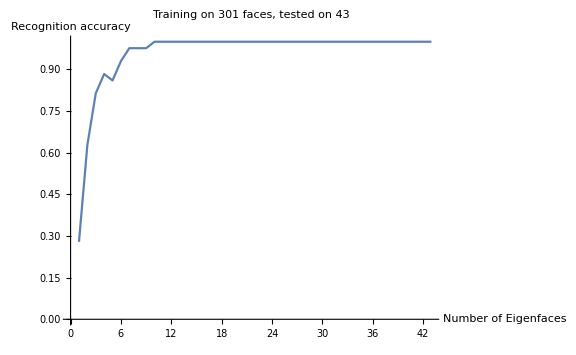

```mathematica
ListLinePlot[data2,PlotRange->{{0,All},{0,1}},ImageSize->Large,AxesLabel->{"Number of Eigenfaces","Recognition accuracy"},PlotLabel->"Training on "<>ToString@Length@training2<>" faces, tested on "<>ToString@Length@testing2]
```

```mathematica
makeGrid[training2,testing2,All]
```

```mathematica
emotions
```

{Neutral,Happy,Winking,Angry,Sad,Concerned,Disgusted,Surprised}

## Work with fewer people

```mathematica
Length@images
```

```mathematica
training3=labelledFaces[[1;;40;;8]];
testing3=labelledFaces[[Complement[Range[40],Range[40,8]]]];
training4=labelledFaces[[Complement[Range[40],Range[3,40,8]]]];
testing4=labelledFaces[[3;;40;;8]];
```

### Train on few

```mathematica
data3=FOM[training3,training3,testing3,{1,5}];
Dimensions@data3
```

{5}

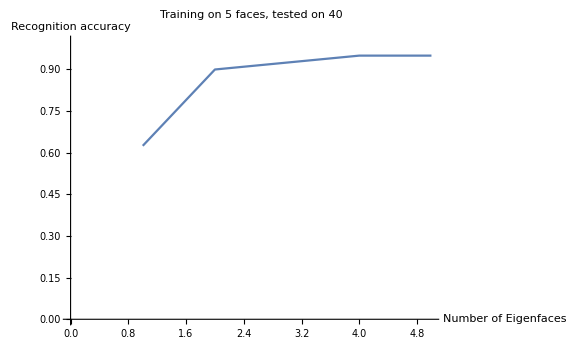

```mathematica
ListLinePlot[data3,PlotRange->{{0,All},{0,1}},ImageSize->Large,AxesLabel->{"Number of Eigenfaces","Recognition accuracy"},PlotLabel->"Training on "<>ToString@Length@training3<>" faces, tested on "<>ToString@Length@testing3]
```

```mathematica
makeGrid[training2,testing2,All]
```

```mathematica
emotions
```

{Neutral,Happy,Winking,Angry,Sad,Concerned,Disgusted,Surprised}

### Train on many

```mathematica
data3=FOM[training3,training4,testing4,{1,5}];
Dimensions@data3
```

{5}

```mathematica
ListLinePlot[data3,PlotRange->{{0,All},{0,1}},ImageSize->Large,AxesLabel->{"Number of Eigenfaces","Recognition accuracy"},PlotLabel->"Training on "<>ToString@Length@training3<>" faces, tested on "<>ToString@Length@testing3]
```

-Graphics-

```mathematica
makeGrid[training2,testing2,All]
```

```mathematica
emotions
```

{Neutral,Happy,Winking,Angry,Sad,Concerned,Disgusted,Surprised}